## Star - Disk magnetic field interaction

### Setup

```mathematica
$HistoryLength=0;ClearAll["Global`*"]; 
SetDirectory["/home/dagl4841/ResearchLocal/netFieldEvo/mathematica"];
```

```mathematica
rloglog[functions_,yLabel_,legendLabels_,coords_]:=LogLogPlot[functions, {r,rMin,rMax}, Frame->True,FrameLabel->{"r (AU)", yLabel},ImageSize->Large,PlotLegends->legendLabels,BaseStyle->{FontWeight->"Bold",FontSize->14},PlotRange->Full, GridLines->coords]
au=1.5*10^13;
G=6.67*10^-8;
Msun=2*10^33;
mp=1*10^-24;
kb=1.38*10^-16;
year=3.15*10^7;
σ = 5.67*10^-5;
rMin=r0star;
rMax=10;
```

```mathematica
starSizeFactor=0.1;
Mstar=starSizeFactor*Msun;
```

### Stellar field

```mathematica
r0star=starSizeFactor*0.0046; (* 1/200 of an AU is roughly photosphere *)
```

### MMSN model

```mathematica
(* input r is in au, other quantities are in cm *)
diskMassFraction = 0.024033; (* within 100 AU for MMSN is 0.024033 *)
r0disk=1;
Lfactor=10^-3;
μ=2.7;
Σ[r_]:=(diskMassFraction/0.024033*Mstar/Msun)1700* (r/r0disk)^(-3/2); 
T[r_]:=280*(r/r0disk)^(-1/2)*(Lfactor)^(1/4);
cs[r_]:=√((kb T[r])/(μ mp)) ;
Ω[r_]:=√((G Mstar)/(r*au)^3)
h[r_]:=cs[r]/Ω[r];
hor[r_]:=h[r]/(r*au)
ρ[r_]:=1/(√(2π))Σ[r]/h[r];
P[r_]:=ρ[r]*cs[r]^2;
```

```mathematica
rDZ=Solve[T[r]==800,r][[1,1,2]]//N
```

0.00387379

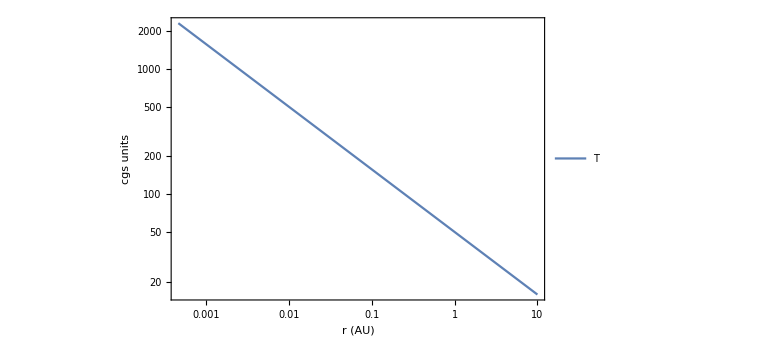

```mathematica
rloglog[{T[r]}, "cgs units",{"T"},{{rDZ},{1000}}]
```

### Chiang-Goldreich model (valid between 0.4 au and 84 au), from phil’s text p. 50

```mathematica
(* input r is in au, other quantities are in cm *)
μ=2.7;
Tcg[r_]:=150*(r/1)^(-3/7)
```

```mathematica
rDZ=Solve[Tcg[r]==800,r][[1,1,2]]//N
```

0.0201219

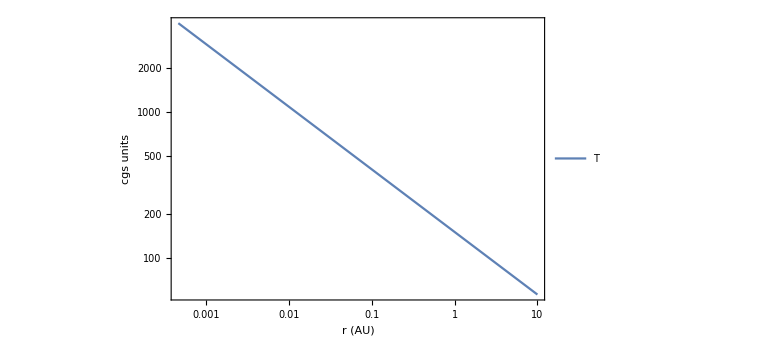

```mathematica
rloglog[{Tcg[r]}, "cgs units",{"T"},{{rDZ,0.4},{1000}}]
```

### Active Disk (phil’s text p. 75). also see Garaud and Lin 2007

```mathematica
(* input r is in au, other quantities are in cm *)
Td[r_,Mdot_]:=((3G Mstar Mdot*Msun/year)/(8 π σ (r*au)^3)(1-√((r0star*au)/(r*au))))^(1/4)
Tc[r_,Mdot_]:=(3/4 τ[r] )^(1/4)Td[r,Mdot]
τ[r_]:=1/2 Σ[r]κR[r]
κR[r_]:=3
```

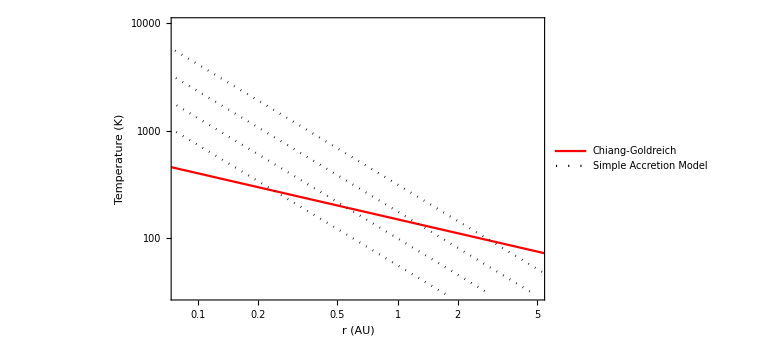

TemperatureProfiles.png

```mathematica
plt=LogLogPlot[
{Tcg[r],Tc[r,10^-7],Tc[r,10^-8],Tc[r,10^-9],Tc[r,10^-10]}, {r,rMin,rMax},
 Frame->True,FrameLabel->{"r (AU)", "Temperature (K)"},
ImageSize->Large,
PlotLegends->Placed[{"Chiang-Goldreich","Simple Accretion Model"},{0.75,0.87}],
BaseStyle->{FontWeight->"Normal",FontSize->14},
PlotRange->{{0.08,5},{30,10000}},
 GridLines->{{},{1000}}, 
GridLinesStyle->{{Gray},{Gray}},
PlotStyle->{{Red},{Black, Dotted},{Black, Dotted},{Black, Dotted},{Black, Dotted},{Black, Dotted},{Black, Dotted}}
]
Export["TemperatureProfiles.png",plt]
```